Formulation of the nonlinear equations of motion

Guilherme Rocha Martins^a, Paulo Akira Figuti Enabe^a,Rodrigo Provasi Correia^a,Alfredo Gay Neto^a
a. Offshore Mechanics Laboratory - Escola Politécnica, Universidade de São Paulo
b. Computational Mechanics Laboratory - Escola Politécnica, Universidade de São Paulo

This short code evaluates the nonlinear equations of motions of the reduced-order model (ROM) of a parametric excitation phenomenon.
The mainly advantage is to use the Wolphram Mathematica powerfull symbolic computation to easily identify the nondimensional quantities

```mathematica
ClearAll["Global`*"]

(* Shape functions *)
Subscript[ψ, 1][z_]:=Sin[(1 π)/L z]
Subscript[ψ, 2][z_]:=Sin[(2 π)/L z]
Subscript[ψ, 3][z_]:=Sin[(3 π)/L z]

(* Normal force over the length (z) and time (t) *)
T[z_,t_]:=Subscript[T, top]-γ*L+γ *z+EA/L Subscript[A, top] Cos[Ω t]
(* Temporal-spatial separation *)
x[z_,t_]:=Subscript[ψ, 1][z]×Subscript[A, 1][t]+Subscript[ψ, 2][z]×Subscript[A, 2][t]+Subscript[ψ, 3][z]×Subscript[A, 3][t]


(* Number that appears in some divisors *)
div:=m*Subscript[ω, 1]^2+Subscript[m, a]*Subscript[ω, 1]^2


(* Evaluate the equations of motion *)
eq1=Collect[Integrate[  ( D[x[z,t],{t,2}]+  (c Subscript[ω, 1])/div D[x[z,t],{t,1}]+EI/div D[x[z,t],{z,4}]+1/div(-γ D[x[z, t],{z,1}]-D[x[z, t],{z,2}] (Subscript[T, top]-γ L+γ z)-EA/L Subscript[A, top] Cos[Ω t] D[x[z, t],{z,2}])-d^2/div EA/(2 L) D[x[z,t],{z,2}] Integrate[(D[x[z,t],{z,1}])^2,{z,0,L}]) Subscript[ψ, 1][z] 2/L,{z,0,L}],
(*Coef. to try to collect*){(Subscript[A, 1][t])^2 Subscript[A, 2][t],(Subscript[A, 1][t])^2 Subscript[A, 3][t],(Subscript[A, 2][t])^2 Subscript[A, 3][t],Subscript[A, 1][t] (Subscript[A, 2][t])^2,Subscript[A, 1][t] (Subscript[A, 3][t])^2,Subscript[A, 2][t] (Subscript[A, 3][t])^2,Subscript[A, 2][t] Subscript[A, 3][t],Subscript[A, 1][t] Subscript[A, 2][t],Subscript[A, 1][t] Subscript[A, 3][t],
(Subscript[A, 1][t])^2,(Subscript[A, 2][t])^2,(Subscript[A, 3][t])^2,(Subscript[A, 1][t])^3,(Subscript[A, 2][t])^3,(Subscript[A, 3][t])^3,Subscript[A, 1][t],Subscript[A, 2][t],Subscript[A, 3][t],Subscript[A, 1]'[t],Subscript[A, 2]'[t],Subscript[A, 3]'[t]},FullSimplify];
eq2=Collect[Integrate[  ( D[x[z,t],{t,2}]+  (c Subscript[ω, 1])/div D[x[z,t],{t,1}]+EI/div D[x[z,t],{z,4}]+1/div(-γ D[x[z, t],{z,1}]-D[x[z, t],{z,2}] (Subscript[T, top]-γ L+γ z)-EA/L Subscript[A, top] Cos[Ω t] D[x[z, t],{z,2}])-d^2/div EA/(2 L) D[x[z,t],{z,2}] Integrate[(D[x[z,t],{z,1}])^2,{z,0,L}]) Subscript[ψ, 2][z] 2/L,{z,0,L}],
(*Coef. to try to collect*){(Subscript[A, 1][t])^2 Subscript[A, 2][t],(Subscript[A, 1][t])^2 Subscript[A, 3][t],(Subscript[A, 2][t])^2 Subscript[A, 3][t],Subscript[A, 1][t] (Subscript[A, 2][t])^2,Subscript[A, 1][t] (Subscript[A, 3][t])^2,Subscript[A, 2][t] (Subscript[A, 3][t])^2,Subscript[A, 2][t] Subscript[A, 3][t],Subscript[A, 1][t] Subscript[A, 2][t],Subscript[A, 1][t] Subscript[A, 3][t],
(Subscript[A, 1][t])^2,(Subscript[A, 2][t])^2,(Subscript[A, 3][t])^2,(Subscript[A, 1][t])^3,(Subscript[A, 2][t])^3,(Subscript[A, 3][t])^3,Subscript[A, 1][t],Subscript[A, 2][t],Subscript[A, 3][t],Subscript[A, 1]'[t],Subscript[A, 2]'[t],Subscript[A, 3]'[t]},FullSimplify];
eq3=Collect[Integrate[  ( D[x[z,t],{t,2}]+  (c Subscript[ω, 1])/div D[x[z,t],{t,1}]+EI/div D[x[z,t],{z,4}]+1/div(-γ*D[x[z, t],{z,1}]-D[x[z, t],{z,2}] (Subscript[T, top]-γ L+γ z)-EA/L Subscript[A, top] Cos[Ω t] D[x[z, t],{z,2}])-d^2/div EA/(2 L) D[x[z,t],{z,2}] Integrate[(D[x[z,t],{z,1}])^2,{z,0,L}]) Subscript[ψ, 3][z] 2/L,{z,0,L}],
(*Coef. to try to collect*){(Subscript[A, 1][t])^2 Subscript[A, 2][t],(Subscript[A, 1][t])^2 Subscript[A, 3][t],(Subscript[A, 2][t])^2 Subscript[A, 3][t],Subscript[A, 1][t] (Subscript[A, 2][t])^2,Subscript[A, 1][t] (Subscript[A, 3][t])^2,Subscript[A, 2][t] (Subscript[A, 3][t])^2,Subscript[A, 2][t] Subscript[A, 3][t],Subscript[A, 1][t] Subscript[A, 2][t],Subscript[A, 1][t] Subscript[A, 3][t],
(Subscript[A, 1][t])^2,(Subscript[A, 2][t])^2,(Subscript[A, 3][t])^2,(Subscript[A, 1][t])^3,(Subscript[A, 2][t])^3,(Subscript[A, 3][t])^3,Subscript[A, 1][t],Subscript[A, 2][t],Subscript[A, 3][t],Subscript[A, 1]'[t],Subscript[A, 2]'[t],Subscript[A, 3]'[t]},FullSimplify];
```

```mathematica
(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *
 *  Show the equations of motion in 'Traditional form' and in 'Tex form'   *
 * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)


(* Output formatting *)
styleTitle=Style[#,FontSize->20,FontWeight->Bold,Background->LightBlue,FontFamily->"Times New Roman"]&;
styleTeX=Style[#,FontSize->20,FontWeight->Bold,Background->LightRed,FontFamily->"Times New Roman"]&;
styleText=Style[#,FontSize->16,FontWeight->Bold,FontFamily->"Times New Roman"]&;
styleEqs=Style[#,FontSize->14,FontFamily->"Cambria Math"]&;

(* Result in traditional form *)
Print[styleTitle@"Equations of motion: \n\n",
styleText@" - First equation of motion: \n",styleEqs@ TraditionalForm[eq1],"\n\n",
styleText@" - Second equation of motion: \n", styleEqs@TraditionalForm[eq2],"\n\n",
styleText@" - Third equation of motion: \n", styleEqs@TraditionalForm[eq3],"\n"
](*End print*)

Print["\n"]

(* TeX format *)
Print[styleTeX@"Equations in TeX format: \n\n",
styleText@" - First equation of motion: \n", styleEqs@TeXForm[eq1],"\n\n",
styleText@" - Second equation of motion: \n",styleEqs@ TeXForm[eq2],"\n\n",
styleText@" - Third equation of motion: \n",styleEqs@ TeXForm[eq3], "\n"
](*End print*)
```

Equations of motion: 

 - First equation of motion: 
(c A_1'(t))/(ω_1 (m_a+m))+A_1(t) ((π^4 d^2 EA (A_2(t))^2)/(L^4 ω_1^2 (m_a+m))+(9 π^4 d^2 EA (A_3(t))^2)/(4 L^4 ω_1^2 (m_a+m))+(π^2 (2 L (EA A_top cos(t Ω)+L T_top)+2 π^2 EI-γ L^3))/(2 L^4 ω_1^2 (m_a+m)))+(π^4 d^2 EA (A_1(t))^3)/(4 L^4 ω_1^2 (m_a+m))-(40 γ A_2(t))/(9 L ω_1^2 (m_a+m))+A_1''(t)

 - Second equation of motion: 
(c A_2'(t))/(ω_1 (m_a+m))+A_2(t) ((9 π^4 d^2 EA (A_3(t))^2)/(L^4 ω_1^2 (m_a+m))+(2 π^2 (2 L (EA A_top cos(t Ω)+L T_top)+8 π^2 EI-γ L^3))/(L^4 ω_1^2 (m_a+m)))+(4 π^4 d^2 EA (A_2(t))^3)/(L^4 ω_1^2 (m_a+m))+(π^4 d^2 EA (A_1(t))^2 A_2(t))/(L^4 ω_1^2 (m_a+m))-(40 γ A_1(t))/(9 L ω_1^2 (m_a+m))-(312 γ A_3(t))/(25 L ω_1^2 (m_a+m))+A_2''(t)

 - Third equation of motion: 
(c A_3'(t))/(ω_1 (m_a+m))+(81 π^4 d^2 EA (A_3(t))^3)/(4 L^4 ω_1^2 (m_a+m))+(9 π^4 d^2 EA (A_1(t))^2 A_3(t))/(4 L^4 ω_1^2 (m_a+m))+(9 π^4 d^2 EA (A_2(t))^2 A_3(t))/(L^4 ω_1^2 (m_a+m))+(9 π^2 A_3(t) (2 L (EA A_top cos(t Ω)+L T_top)+18 π^2 EI-γ L^3))/(2 L^4 ω_1^2 (m_a+m))-(312 γ A_2(t))/(25 L ω_1^2 (m_a+m))+A_3''(t)

Equations in TeX format: 

 - First equation of motion: 
\frac{c A_1'(t)}{\omega _1 \left(m_a+m\right)}+A_1(t) \left(\frac{\pi ^4 d^2 \text{EA} A_2(t){}^2}{L^4 \omega _1^2 \left(m_a+m\right)}+\frac{9 \pi ^4 d^2 \text{EA} A_3(t){}^2}{4 L^4 \omega _1^2 \left(m_a+m\right)}+\frac{\pi ^2 \left(2 L \left(\text{EA} A_{\text{top}} \cos (t \Omega )+L T_{\text{top}}\right)+2 \pi ^2 \text{EI}-\gamma  L^3\right)}{2 L^4 \omega _1^2 \left(m_a+m\right)}\right)+\frac{\pi ^4 d^2 \text{EA} A_1(t){}^3}{4 L^4 \omega _1^2 \left(m_a+m\right)}-\frac{40 \gamma  A_2(t)}{9 L \omega _1^2 \left(m_a+m\right)}+A_1''(t)

 - Second equation of motion: 
\frac{c A_2'(t)}{\omega _1 \left(m_a+m\right)}+A_2(t) \left(\frac{9 \pi ^4 d^2 \text{EA} A_3(t){}^2}{L^4 \omega _1^2 \left(m_a+m\right)}+\frac{2 \pi ^2 \left(2 L \left(\text{EA} A_{\text{top}} \cos (t \Omega )+L T_{\text{top}}\right)+8 \pi ^2 \text{EI}-\gamma  L^3\right)}{L^4 \omega _1^2 \left(m_a+m\right)}\right)+\frac{4 \pi ^4 d^2 \text{EA} A_2(t){}^3}{L^4 \omega _1^2 \left(m_a+m\right)}+\frac{\pi ^4 d^2 \text{EA} A_1(t){}^2 A_2(t)}{L^4 \omega _1^2 \left(m_a+m\right)}-\frac{40 \gamma  A_1(t)}{9 L \omega _1^2 \left(m_a+m\right)}-\frac{312 \gamma  A_3(t)}{25 L \omega _1^2 \left(m_a+m\right)}+A_2''(t)

 - Third equation of motion: 
\frac{c A_3'(t)}{\omega _1 \left(m_a+m\right)}+\frac{81 \pi ^4 d^2 \text{EA} A_3(t){}^3}{4 L^4 \omega _1^2 \left(m_a+m\right)}+\frac{9 \pi ^4 d^2 \text{EA} A_1(t){}^2 A_3(t)}{4 L^4 \omega _1^2 \left(m_a+m\right)}+\frac{9 \pi ^4 d^2 \text{EA} A_2(t){}^2 A_3(t)}{L^4 \omega _1^2 \left(m_a+m\right)}+\frac{9 \pi ^2 A_3(t) \left(2 L \left(\text{EA} A_{\text{top}} \cos (t \Omega )+L T_{\text{top}}\right)+18 \pi ^2 \text{EI}-\gamma  L^3\right)}{2 L^4 \omega _1^2 \left(m_a+m\right)}-\frac{312 \gamma  A_2(t)}{25 L \omega _1^2 \left(m_a+m\right)}+A_3''(t)

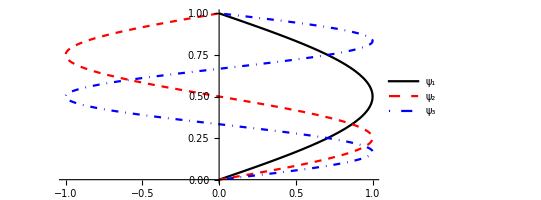

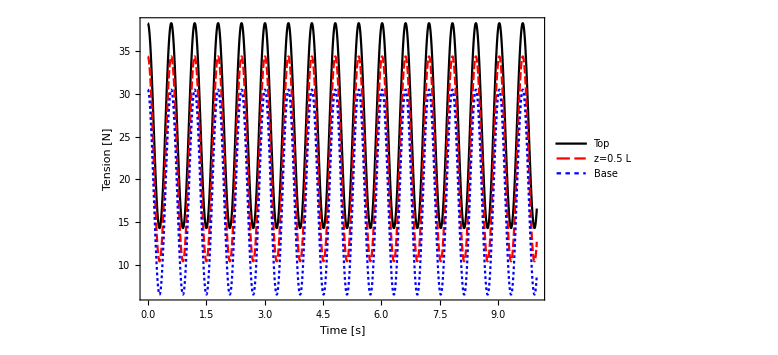

```mathematica
L:=1 (*normalized*)
paramPlot=ParametricPlot[{{Subscript[ψ, 1][z],z},{Subscript[ψ, 2][z],z},{Subscript[ψ, 3][z],z}},{z,0,L},
PlotStyle->{Black,{Red,Dashed},{Blue,DotDashed}},PlotLegends->{"ψ_1","ψ_2","ψ_3"}]


  (**************************
 * Basic graphics formatting *
 **************************)

AxisFontSize=20;NumberSize=18;LegendFontSize=16;
font="Times New Roman";

(*Parameters of the specific problem studied*)
n=2;
Subscript[T, top]=38.36; Ω=n*2*π*0.83;
γ=1.19*9.81-1025*9.81*π*(22.2/1000)^2/4;
L=2.552;EA=1200;Subscript[A, top] =0.01*2.552;


Plot[{T[1,t],T[0.5,t],T[0,t]},{t,0,10},
Axes->False,Frame->True,
FrameLabel->{{Style["Tension  [N]",FontSize->AxisFontSize,FontFamily->font],None},{Style["Time  [s]",FontSize->AxisFontSize,FontFamily->font],None}},
FrameStyle->Directive[Black,FontSize->NumberSize,FontFamily->font],ImageSize->Large,
PlotStyle->{Black,{Red},{Blue},{Green}},PlotLegends->{"Top","z=0.5 L","Base"}]
```